```mathematica
dirStr = NotebookDirectory[]~StringJoin~"Utils.nb";

NotebookEvaluate[dirStr];
NotebookEvaluate[dirStr];
```

```mathematica
(*We specify the Hamiltonian in pieces*)
term1 = p[1]^2/(2m) + 1/2 m ω[1]^2 q[1]^2;
term2 = 0;
term3 = g4[1] q[1]^4;

(*term1 = p[1]^2/(2m) + 1/2 m ω[1]^2 q[1]^2 + p[2]^2/(2m) + 1/2 m ω[2]^2 q[2]^2 + p[3]^2/(2m) + 1/2 m ω[3]^2 q[3]^2;
term2 = 0;
term3 = g4[1] q[1]^4 /4! + g4[2] q[2]^4 /4! + g4[3] q[3]^4 /4! + λ4[1, 2] q[1]^2 q[2]^2 /4! + + λ4[1, 3] q[1]^2 q[3]^2 /4!;*)

eigs = {ω[1]};
prs = {{p[1], q[1]}};

(*eigs = {ω[1], ω[2], ω[3]};
prs = {{p[1], q[1]}, {p[2], q[2]}, {p[3], q[3]}};*)

(*Some symplectic transformations used below. x' = (x - I p)/√2 = Sqrt[ℏ] a^† (the raising operator).
Similarly, p' = (p - I x)/√2 = -I Sqrt[ℏ] a (lowering operator).*)
scaleRule = {q[1] -> q[1]/Sqrt[m ω[1]],
			p[1] -> Sqrt[m ω[1]]p[1]};
diagRule = {q[1] -> 1/Sqrt[2](q[1] + I p[1]),
			p[1] -> 1/Sqrt[2](p[1] + I q[1])};

(*scaleRule = {q[1] -> q[1]/Sqrt[m ω[1]],
			p[1] -> Sqrt[m ω[1]]p[1],
			q[2] -> q[2]/Sqrt[m ω[2]],
			p[2] -> Sqrt[m ω[2]]p[2],
			q[3] -> q[3]/Sqrt[m ω[3]],
			p[3] -> Sqrt[m ω[3]]p[3]};
diagRule = {q[1] -> 1/Sqrt[2](q[1] + I p[1]),
			p[1] -> 1/Sqrt[2](p[1] + I q[1]),
			q[2] -> 1/Sqrt[2](q[2] + I p[2]),
			p[2] -> 1/Sqrt[2](p[2] + I q[2]),
			q[3] -> 1/Sqrt[2](q[3] + I p[3]),
			p[3] -> 1/Sqrt[2](p[3] + I q[3])};*)

(*Choose degeneracy:*)
(*Ω = ω;*)

(*We rescale and diagonalize the Hamiltonian, what we obtain we assign to H[n, m].
Here, n is the order of the term and m is the order of the QNF, which starts at 2.*)
H[0, 2] = 0;
H[1, 2] = 0;
H[2, 2] = Expand[term1 /. scaleRule /. diagRule];
H[3, 2] = Expand[term2 /. scaleRule /. diagRule];
H[4, 2] = Expand[term3 /. scaleRule /. diagRule];
H[n_ ? (# > 4 &), 2] := 0;

H[2, 2]
H[3, 2]
H[4, 2]

QNFOrd = 18;
QNFSymb = computeQNFSymbUpToOrder[QNFOrd]

Table[{k - 1, MB[QNFSymb[[3]], QNFSymb[[k]]]}, {k, 5, Length[QNFSymb], 2}]
```

ⅈ p[1] q[1] ω[1]

0

(g4[1] p[1]^4)/(4 m^2 ω[1]^2)-(ⅈ g4[1] p[1]^3 q[1])/(m^2 ω[1]^2)-(3 g4[1] p[1]^2 q[1]^2)/(2 m^2 ω[1]^2)+(ⅈ g4[1] p[1] q[1]^3)/(m^2 ω[1]^2)+(g4[1] q[1]^4)/(4 m^2 ω[1]^2)

{0,0,ⅈ p[1] q[1] ω[1],0,-(3 g4[1] p[1]^2 q[1]^2)/(2 m^2 ω[1]^2),0,(9 ⅈ ℏ^2 g4[1]^2 p[1] q[1])/(8 m^4 ω[1]^5)+(17 ⅈ g4[1]^2 p[1]^3 q[1]^3)/(4 m^4 ω[1]^5),0,(459 ℏ^2 g4[1]^3 p[1]^2 q[1]^2)/(16 m^6 ω[1]^8)+(375 g4[1]^3 p[1]^4 q[1]^4)/(16 m^6 ω[1]^8),0,-(4095 ⅈ ℏ^4 g4[1]^4 p[1] q[1])/(64 m^8 ω[1]^11)-(35585 ⅈ ℏ^2 g4[1]^4 p[1]^3 q[1]^3)/(64 m^8 ω[1]^11)-(10689 ⅈ g4[1]^4 p[1]^5 q[1]^5)/(64 m^8 ω[1]^11),0,-(1352457 ℏ^4 g4[1]^5 p[1]^2 q[1]^2)/(256 m^10 ω[1]^14)-(2466135 ℏ^2 g4[1]^5 p[1]^4 q[1]^4)/(256 m^10 ω[1]^14)-(87549 g4[1]^5 p[1]^6 q[1]^6)/(64 m^10 ω[1]^14),0,(16585569 ⅈ ℏ^6 g4[1]^6 p[1] q[1])/(1024 m^12 ω[1]^17)+(30562913 ⅈ ℏ^4 g4[1]^6 p[1]^3 q[1]^3)/(128 m^12 ω[1]^17)+(40194609 ⅈ ℏ^2 g4[1]^6 p[1]^5 q[1]^5)/(256 m^12 ω[1]^17)+(3132399 ⅈ g4[1]^6 p[1]^7 q[1]^7)/(256 m^12 ω[1]^17),0,(2723363397 ℏ^6 g4[1]^7 p[1]^2 q[1]^2)/(1024 m^14 ω[1]^20)+(8222406045 ℏ^4 g4[1]^7 p[1]^4 q[1]^4)/(1024 m^14 ω[1]^20)+(2521828953 ℏ^2 g4[1]^7 p[1]^6 q[1]^6)/(1024 m^14 ω[1]^20)+(238225977 g4[1]^7 p[1]^8 q[1]^8)/(2048 m^14 ω[1]^20),0,-(157429710009 ⅈ ℏ^8 g4[1]^8 p[1] q[1])/(16384 m^16 ω[1]^23)-(863107544161 ⅈ ℏ^6 g4[1]^8 p[1]^3 q[1]^3)/(4096 m^16 ω[1]^23)-(924767616969 ⅈ ℏ^4 g4[1]^8 p[1]^5 q[1]^5)/(4096 m^16 ω[1]^23)-(308236310373 ⅈ ℏ^2 g4[1]^8 p[1]^7 q[1]^7)/(8192 m^16 ω[1]^23)-(18945961925 ⅈ g4[1]^8 p[1]^9 q[1]^9)/(16384 m^16 ω[1]^23)}

{{4,0},{6,0},{8,0},{10,0},{12,0},{14,0},{16,0},{18,0}}

```mathematica
(*ClearAll[quant];
quant[m_, n_, {P_, Q_}] := Sum[1/2^n Binomial[n, k1] NonCommutativeMultiply @@ (Table[Q, {k2, 1, k1}]~Join~Table[P, {k2, 1, m}]~Join~Table[Q, {k2, 1, n-k1}]), {k1, 0, n}];
quant[1, 0, {P_, Q_}] := P;
quant[0, 1, {P_, Q_}] := Q;
quant[0, 0, {P_, Q_}] := 1;

ClearAll[coeffToQuant];
coeffToQuant[powVec_] := Module[{prods = {}, length},
	Do[
		prods = Append[prods, quant[powVec[[2k - 1]], powVec[[2k]], prs[[k]]]],
		{k, 1, Length[prs]}
	];
	
	prods = DeleteElements[prods, {1}];
	
	length = Length[prods];
	Return[
		Which[
			length > 1, NonCommutativeMultiply @@ prods,
			length == 1, First @ prods,
			length == 0, 1
		]
	]
];

ClearAll[WignerWeylQuant];
WignerWeylQuant[expr_] := Module[
	{coeffRules = CoefficientRules[expr, Flatten[prs]], coeffs, monoms, quantMonoms, res},
	coeffs = Part[#, 2] & /@ coeffRules;
	monoms = Part[#, 1] & /@ coeffRules;
	quantMonoms = coeffToQuant /@ monoms;
	res = Sum[coeffs[[k]]quantMonoms[[k]], {k, 1, Length[coeffs]}];
	Return[res]
];

QNF = WignerWeylQuant /@ QNFSymb

Needs["NC`"];
Needs["NCAlgebra`"];

SetCommutative[{m, ℏ, g3, λ3, g4, λ4, ω}];
SetNonCommutative[{p, q}];

QNF = NCExpand[QNF]*)
```

```mathematica
(*(*Takes into account that p = -I Sqrt[ℏ] a and q = Sqrt[ℏ] a^†, hence because [a, a^†] = 1: p ** q = q ** p - I ℏ.*)
SetNonCommutative[left, right];
ClearAll[nrmOrdRule];
nrmOrdRule = Table[
	NonCommutativeMultiply[left___, prs[[k, 1]], prs[[k, 2]], right___] ->
	NonCommutativeMultiply[left, prs[[k, 2]], prs[[k, 1]], right] +
	(-I ℏ) NonCommutativeMultiply[left, right],
	{k, 1, Length[prs]}
];

ClearAll[needsReordering];
needsReordering[op1_, op2_] := Position[prs, op1][[1, 1]] > Position[prs, op2][[1, 1]];

ClearAll[commuteRule];
commuteRule = {
	NonCommutativeMultiply[left___, s1_, s2_, right___] /; needsReordering[s1, s2] :>
	NonCommutativeMultiply[left, s2, s1, right]
};

ClearAll[joinedRule];
joinedRule = commuteRule~Join~nrmOrdRule;

QNFNormalOrdered = NCExpand[QNF //. joinedRule]*)
```

```mathematica
(*(*Verifies whether the Hamiltonian is still in NF.*)
commuteNO[expr1_, expr2_] := NCExpand[NCExpand[expr1 ** expr2] //. joinedRule] - NCExpand[NCExpand[expr2 ** expr1] //. joinedRule];

Table[{k - 1, commuteNO[QNFNormalOrdered[[3]], QNFNormalOrdered[[k]]]}, {k, 5, Length[QNFNormalOrdered], 2}]*)
```

```mathematica
(*Module[
	{rule = symbRule[59], ruleInv = symbRuleInv[59], terms, flat},
	flat = Flatten @ (Last /@ rule);
	SetNonCommutative[flat];
	terms = Total[QNFNormalOrdered]/.rule;
	coeffs = NCCoefficientList[terms, flat];
	monoms = NCMonomialList[terms, flat]//.ruleInv;
];

ClearAll[matrixElement, n, m]
matrixElement[mon_] := Module[{pl, pr},
	Do[Subscript[pl, k] = Count[Cases[mon, _, Infinity], prs[[k, 1]]], {k, 1, Length[prs]}];
	Do[Subscript[pr, k] = Count[Cases[mon, _, Infinity], prs[[k, 2]]], {k, 1, Length[prs]}];

	Return[
		(*Product[(Sqrt[ℏ]^Subscript[pr, k] (-I Sqrt[ℏ])^Subscript[pl, k]) Sqrt[(Subscript[m, k]!/(Subscript[m, k]-Subscript[pr, k])!)] Sqrt[(Subscript[n, k]!/(Subscript[n, k]-Subscript[pl, k])!)] KroneckerDelta[(Subscript[m, k]- Subscript[pr, k]) - (Subscript[n, k] - Subscript[pl, k])], {k, 1, Length[prs]}]*)
		Product[(Sqrt[ℏ]^Subscript[pr, k] (-I Sqrt[ℏ])^Subscript[pl, k]) Sqrt[FactorialPower[Subscript[m, k], Subscript[pr, k]]] Sqrt[FactorialPower[Subscript[n, k], Subscript[pl, k]]] KroneckerDelta[(Subscript[m, k]- Subscript[pr, k]) - (Subscript[n, k] - Subscript[pl, k])], {k, 1, Length[prs]}]
	];
]

HamiltonianMatrixElem = Expand[coeffs . (matrixElement /@ monoms)];

rescaleCouplingsRule = {λ3[1] -> 3! λ3[1], λ3[2] -> 3! λ3[2], g4[1] -> 4! g4[1], g4[2] -> 4! g4[2], λ4 -> 4! λ4};
(groundStateEnergy = HamiltonianMatrixElem /. {Subscript[n, _] -> 0, Subscript[m, _] -> 0}) /. rescaleCouplingsRule

(*SetCommutative[kg, s, m];
unitRule = {m -> kg, ℏ -> kg m^2 s^-1, ω[n_] -> s^-1, g4[n_] -> kg m^-2 s^-2, λ4 -> kg m^-2 s^-2};
groundStateEnergy/.{Plus -> List}/.unitRule*)*)
```

```mathematica
With[{rule = symbRule[45], ruleInv = symbRuleInv[45]},
	ClearAll[JRule];
	JRule = Flatten[Table[{prs[[k, 1]] prs[[k, 2]] -> -I J[k], prs[[k, 1]]^n_ prs[[k, 2]]^n_ -> (-I)^n J[k]^n}, {k, 1, Length[prs]}]] /. rule;
	QNFSymbActions = QNFSymb /. rule //. JRule
]

ClearAll[Op];
Op[J_, n_] := Expand[OverHat[J]Op[J, n-1] + (ℏ/2)^2 (n-1)^2 Op[J, n-2]];
Op[J_, 1] := OverHat[J];
Op[J_, 0] := 1;

ClearAll[opRule];
opRule = {J[m_] -> Op[J[m], 1], J[m_]^n_ :> Op[J[m], n]};

QNFActions = QNFSymbActions /. opRule
QNFActions = Expand[QNFActions]

ClearAll[nRule];
nRule = {OverHat[J[m_]] -> ℏ(n[m] + 1/2)};

QNFExplicitQuantumNumbers = Total[Expand[QNFActions /. nRule]]

groundStateEnergy = QNFExplicitQuantumNumbers /. n[m_] -> 0
```

{0,0,J[1] ω[1],0,(3 g4[1] J[1]^2)/(2 m^2 ω[1]^2),0,(9 ℏ^2 g4[1]^2 J[1])/(8 m^4 ω[1]^5)-(17 g4[1]^2 J[1]^3)/(4 m^4 ω[1]^5),0,-(459 ℏ^2 g4[1]^3 J[1]^2)/(16 m^6 ω[1]^8)+(375 g4[1]^3 J[1]^4)/(16 m^6 ω[1]^8),0,-(4095 ℏ^4 g4[1]^4 J[1])/(64 m^8 ω[1]^11)+(35585 ℏ^2 g4[1]^4 J[1]^3)/(64 m^8 ω[1]^11)-(10689 g4[1]^4 J[1]^5)/(64 m^8 ω[1]^11),0,(1352457 ℏ^4 g4[1]^5 J[1]^2)/(256 m^10 ω[1]^14)-(2466135 ℏ^2 g4[1]^5 J[1]^4)/(256 m^10 ω[1]^14)+(87549 g4[1]^5 J[1]^6)/(64 m^10 ω[1]^14),0,(16585569 ℏ^6 g4[1]^6 J[1])/(1024 m^12 ω[1]^17)-(30562913 ℏ^4 g4[1]^6 J[1]^3)/(128 m^12 ω[1]^17)+(40194609 ℏ^2 g4[1]^6 J[1]^5)/(256 m^12 ω[1]^17)-(3132399 g4[1]^6 J[1]^7)/(256 m^12 ω[1]^17),0,-(2723363397 ℏ^6 g4[1]^7 J[1]^2)/(1024 m^14 ω[1]^20)+(8222406045 ℏ^4 g4[1]^7 J[1]^4)/(1024 m^14 ω[1]^20)-(2521828953 ℏ^2 g4[1]^7 J[1]^6)/(1024 m^14 ω[1]^20)+(238225977 g4[1]^7 J[1]^8)/(2048 m^14 ω[1]^20),0,-(157429710009 ℏ^8 g4[1]^8 J[1])/(16384 m^16 ω[1]^23)+(863107544161 ℏ^6 g4[1]^8 J[1]^3)/(4096 m^16 ω[1]^23)-(924767616969 ℏ^4 g4[1]^8 J[1]^5)/(4096 m^16 ω[1]^23)+(308236310373 ℏ^2 g4[1]^8 J[1]^7)/(8192 m^16 ω[1]^23)-(18945961925 g4[1]^8 J[1]^9)/(16384 m^16 ω[1]^23)}

{0,0,OverHat[J[1]] ω[1],0,(3 g4[1] (ℏ^2/4+OverHat[J[1]]^2))/(2 m^2 ω[1]^2),0,(9 ℏ^2 g4[1]^2 OverHat[J[1]])/(8 m^4 ω[1]^5)-(17 g4[1]^2 (5/4 ℏ^2 OverHat[J[1]]+OverHat[J[1]]^3))/(4 m^4 ω[1]^5),0,-(459 ℏ^2 g4[1]^3 (ℏ^2/4+OverHat[J[1]]^2))/(16 m^6 ω[1]^8)+(375 g4[1]^3 ((9 ℏ^4)/16+7/2 ℏ^2 OverHat[J[1]]^2+OverHat[J[1]]^4))/(16 m^6 ω[1]^8),0,-(4095 ℏ^4 g4[1]^4 OverHat[J[1]])/(64 m^8 ω[1]^11)+(35585 ℏ^2 g4[1]^4 (5/4 ℏ^2 OverHat[J[1]]+OverHat[J[1]]^3))/(64 m^8 ω[1]^11)-(10689 g4[1]^4 (89/16 ℏ^4 OverHat[J[1]]+15/2 ℏ^2 OverHat[J[1]]^3+OverHat[J[1]]^5))/(64 m^8 ω[1]^11),0,(1352457 ℏ^4 g4[1]^5 (ℏ^2/4+OverHat[J[1]]^2))/(256 m^10 ω[1]^14)-(2466135 ℏ^2 g4[1]^5 ((9 ℏ^4)/16+7/2 ℏ^2 OverHat[J[1]]^2+OverHat[J[1]]^4))/(256 m^10 ω[1]^14)+(87549 g4[1]^5 ((225 ℏ^6)/64+439/16 ℏ^4 OverHat[J[1]]^2+55/4 ℏ^2 OverHat[J[1]]^4+OverHat[J[1]]^6))/(64 m^10 ω[1]^14),0,(16585569 ℏ^6 g4[1]^6 OverHat[J[1]])/(1024 m^12 ω[1]^17)-(30562913 ℏ^4 g4[1]^6 (5/4 ℏ^2 OverHat[J[1]]+OverHat[J[1]]^3))/(128 m^12 ω[1]^17)+(40194609 ℏ^2 g4[1]^6 (89/16 ℏ^4 OverHat[J[1]]+15/2 ℏ^2 OverHat[J[1]]^3+OverHat[J[1]]^5))/(256 m^12 ω[1]^17)-(3132399 g4[1]^6 (3429/64 ℏ^6 OverHat[J[1]]+1519/16 ℏ^4 OverHat[J[1]]^3+91/4 ℏ^2 OverHat[J[1]]^5+OverHat[J[1]]^7))/(256 m^12 ω[1]^17),0,-(2723363397 ℏ^6 g4[1]^7 (ℏ^2/4+OverHat[J[1]]^2))/(1024 m^14 ω[1]^20)+(8222406045 ℏ^4 g4[1]^7 ((9 ℏ^4)/16+7/2 ℏ^2 OverHat[J[1]]^2+OverHat[J[1]]^4))/(1024 m^14 ω[1]^20)-(2521828953 ℏ^2 g4[1]^7 ((225 ℏ^6)/64+439/16 ℏ^4 OverHat[J[1]]^2+55/4 ℏ^2 OverHat[J[1]]^4+OverHat[J[1]]^6))/(1024 m^14 ω[1]^20)+(238225977 g4[1]^7 ((11025 ℏ^8)/256+6235/16 ℏ^6 OverHat[J[1]]^2+2107/8 ℏ^4 OverHat[J[1]]^4+35 ℏ^2 OverHat[J[1]]^6+OverHat[J[1]]^8))/(2048 m^14 ω[1]^20),0,-(157429710009 ℏ^8 g4[1]^8 OverHat[J[1]])/(16384 m^16 ω[1]^23)+(863107544161 ℏ^6 g4[1]^8 (5/4 ℏ^2 OverHat[J[1]]+OverHat[J[1]]^3))/(4096 m^16 ω[1]^23)-(924767616969 ℏ^4 g4[1]^8 (89/16 ℏ^4 OverHat[J[1]]+15/2 ℏ^2 OverHat[J[1]]^3+OverHat[J[1]]^5))/(4096 m^16 ω[1]^23)+(308236310373 ℏ^2 g4[1]^8 (3429/64 ℏ^6 OverHat[J[1]]+1519/16 ℏ^4 OverHat[J[1]]^3+91/4 ℏ^2 OverHat[J[1]]^5+OverHat[J[1]]^7))/(8192 m^16 ω[1]^23)-1/(16384 m^16 ω[1]^23)18945961925 g4[1]^8 (230481/256 ℏ^8 OverHat[J[1]]+30539/16 ℏ^6 OverHat[J[1]]^3+5019/8 ℏ^4 OverHat[J[1]]^5+51 ℏ^2 OverHat[J[1]]^7+OverHat[J[1]]^9)}

{0,0,OverHat[J[1]] ω[1],0,(3 ℏ^2 g4[1])/(8 m^2 ω[1]^2)+(3 g4[1] OverHat[J[1]]^2)/(2 m^2 ω[1]^2),0,-(67 ℏ^2 g4[1]^2 OverHat[J[1]])/(16 m^4 ω[1]^5)-(17 g4[1]^2 OverHat[J[1]]^3)/(4 m^4 ω[1]^5),0,(1539 ℏ^4 g4[1]^3)/(256 m^6 ω[1]^8)+(1707 ℏ^2 g4[1]^3 OverHat[J[1]]^2)/(32 m^6 ω[1]^8)+(375 g4[1]^3 OverHat[J[1]]^4)/(16 m^6 ω[1]^8),0,-(305141 ℏ^4 g4[1]^4 OverHat[J[1]])/(1024 m^8 ω[1]^11)-(89165 ℏ^2 g4[1]^4 OverHat[J[1]]^3)/(128 m^8 ω[1]^11)-(10689 g4[1]^4 OverHat[J[1]]^5)/(64 m^8 ω[1]^11),0,(1456569 ℏ^6 g4[1]^5)/(2048 m^10 ω[1]^14)+(9317949 ℏ^4 g4[1]^5 OverHat[J[1]]^2)/(1024 m^10 ω[1]^14)+(587265 ℏ^2 g4[1]^5 OverHat[J[1]]^4)/(64 m^10 ω[1]^14)+(87549 g4[1]^5 OverHat[J[1]]^6)/(64 m^10 ω[1]^14),0,-(1056412343 ℏ^6 g4[1]^6 OverHat[J[1]])/(16384 m^12 ω[1]^17)-(912774217 ℏ^4 g4[1]^6 OverHat[J[1]]^3)/(4096 m^12 ω[1]^17)-(124269873 ℏ^2 g4[1]^6 OverHat[J[1]]^5)/(1024 m^12 ω[1]^17)-(3132399 g4[1]^6 OverHat[J[1]]^7)/(256 m^12 ω[1]^17),0,(106611707169 ℏ^8 g4[1]^7)/(524288 m^14 ω[1]^20)+(104934994197 ℏ^6 g4[1]^7 OverHat[J[1]]^2)/(32768 m^14 ω[1]^20)+(78698260599 ℏ^4 g4[1]^7 OverHat[J[1]]^4)/(16384 m^14 ω[1]^20)+(3294251289 ℏ^2 g4[1]^7 OverHat[J[1]]^6)/(2048 m^14 ω[1]^20)+(238225977 g4[1]^7 OverHat[J[1]]^8)/(2048 m^14 ω[1]^20),0,-(114146479775437 ℏ^8 g4[1]^8 OverHat[J[1]])/(4194304 m^16 ω[1]^23)-(30818393633217 ℏ^6 g4[1]^8 OverHat[J[1]]^3)/(262144 m^16 ω[1]^23)-(12484329668811 ℏ^4 g4[1]^8 OverHat[J[1]]^5)/(131072 m^16 ω[1]^23)-(349771437429 ℏ^2 g4[1]^8 OverHat[J[1]]^7)/(16384 m^16 ω[1]^23)-(18945961925 g4[1]^8 OverHat[J[1]]^9)/(16384 m^16 ω[1]^23)}

-(1030495099053 ℏ^9 g4[1]^8)/(32768 m^16 ω[1]^23)-(4834176671621 ℏ^9 g4[1]^8 n[1])/(32768 m^16 ω[1]^23)-(2537383485735 ℏ^9 g4[1]^8 n[1]^2)/(8192 m^16 ω[1]^23)-(3308747108991 ℏ^9 g4[1]^8 n[1]^3)/(8192 m^16 ω[1]^23)-(5506202785335 ℏ^9 g4[1]^8 n[1]^4)/(16384 m^16 ω[1]^23)-(3546040705263 ℏ^9 g4[1]^8 n[1]^5)/(16384 m^16 ω[1]^23)-(711566315607 ℏ^9 g4[1]^8 n[1]^6)/(8192 m^16 ω[1]^23)-(260142547377 ℏ^9 g4[1]^8 n[1]^7)/(8192 m^16 ω[1]^23)-(170513657325 ℏ^9 g4[1]^8 n[1]^8)/(32768 m^16 ω[1]^23)-(18945961925 ℏ^9 g4[1]^8 n[1]^9)/(16384 m^16 ω[1]^23)+(2723294673 ℏ^8 g4[1]^7)/(2048 m^14 ω[1]^20)+(12109639665 ℏ^8 g4[1]^7 n[1])/(2048 m^14 ω[1]^20)+(3063368181 ℏ^8 g4[1]^7 n[1]^2)/(256 m^14 ω[1]^20)+(442610763 ℏ^8 g4[1]^7 n[1]^3)/(32 m^14 ω[1]^20)+(11616481779 ℏ^8 g4[1]^7 n[1]^4)/(1024 m^14 ω[1]^20)+(5775167853 ℏ^8 g4[1]^7 n[1]^5)/(1024 m^14 ω[1]^20)+(620229141 ℏ^8 g4[1]^7 n[1]^6)/(256 m^14 ω[1]^20)+(238225977 ℏ^8 g4[1]^7 n[1]^7)/(512 m^14 ω[1]^20)+(238225977 ℏ^8 g4[1]^7 n[1]^8)/(2048 m^14 ω[1]^20)-(65518401 ℏ^7 g4[1]^6)/(1024 m^12 ω[1]^17)-(277375697 ℏ^7 g4[1]^6 n[1])/(1024 m^12 ω[1]^17)-(126462555 ℏ^7 g4[1]^6 n[1]^2)/(256 m^12 ω[1]^17)-(70784591 ℏ^7 g4[1]^6 n[1]^3)/(128 m^12 ω[1]^17)-(365491665 ℏ^7 g4[1]^6 n[1]^4)/(1024 m^12 ω[1]^17)-(47512563 ℏ^7 g4[1]^6 n[1]^5)/(256 m^12 ω[1]^17)-(21926793 ℏ^7 g4[1]^6 n[1]^6)/(512 m^12 ω[1]^17)-(3132399 ℏ^7 g4[1]^6 n[1]^7)/(256 m^12 ω[1]^17)+(916731 ℏ^6 g4[1]^5)/(256 m^10 ω[1]^14)+(3569679 ℏ^6 g4[1]^5 n[1])/(256 m^10 ω[1]^14)+(3090693 ℏ^6 g4[1]^5 n[1]^2)/(128 m^10 ω[1]^14)+(2786805 ℏ^6 g4[1]^5 n[1]^3)/(128 m^10 ω[1]^14)+(3662295 ℏ^6 g4[1]^5 n[1]^4)/(256 m^10 ω[1]^14)+(262647 ℏ^6 g4[1]^5 n[1]^5)/(64 m^10 ω[1]^14)+(87549 ℏ^6 g4[1]^5 n[1]^6)/(64 m^10 ω[1]^14)-(30885 ℏ^5 g4[1]^4)/(128 m^8 ω[1]^11)-(111697 ℏ^5 g4[1]^4 n[1])/(128 m^8 ω[1]^11)-(80235 ℏ^5 g4[1]^4 n[1]^2)/(64 m^8 ω[1]^11)-(71305 ℏ^5 g4[1]^4 n[1]^3)/(64 m^8 ω[1]^11)-(53445 ℏ^5 g4[1]^4 n[1]^4)/(128 m^8 ω[1]^11)-(10689 ℏ^5 g4[1]^4 n[1]^5)/(64 m^8 ω[1]^11)+(333 ℏ^4 g4[1]^3)/(16 m^6 ω[1]^8)+(1041 ℏ^4 g4[1]^3 n[1])/(16 m^6 ω[1]^8)+(177 ℏ^4 g4[1]^3 n[1]^2)/(2 m^6 ω[1]^8)+(375 ℏ^4 g4[1]^3 n[1]^3)/(8 m^6 ω[1]^8)+(375 ℏ^4 g4[1]^3 n[1]^4)/(16 m^6 ω[1]^8)-(21 ℏ^3 g4[1]^2)/(8 m^4 ω[1]^5)-(59 ℏ^3 g4[1]^2 n[1])/(8 m^4 ω[1]^5)-(51 ℏ^3 g4[1]^2 n[1]^2)/(8 m^4 ω[1]^5)-(17 ℏ^3 g4[1]^2 n[1]^3)/(4 m^4 ω[1]^5)+(3 ℏ^2 g4[1])/(4 m^2 ω[1]^2)+(3 ℏ^2 g4[1] n[1])/(2 m^2 ω[1]^2)+(3 ℏ^2 g4[1] n[1]^2)/(2 m^2 ω[1]^2)+1/2 ℏ ω[1]+ℏ n[1] ω[1]

-(1030495099053 ℏ^9 g4[1]^8)/(32768 m^16 ω[1]^23)+(2723294673 ℏ^8 g4[1]^7)/(2048 m^14 ω[1]^20)-(65518401 ℏ^7 g4[1]^6)/(1024 m^12 ω[1]^17)+(916731 ℏ^6 g4[1]^5)/(256 m^10 ω[1]^14)-(30885 ℏ^5 g4[1]^4)/(128 m^8 ω[1]^11)+(333 ℏ^4 g4[1]^3)/(16 m^6 ω[1]^8)-(21 ℏ^3 g4[1]^2)/(8 m^4 ω[1]^5)+(3 ℏ^2 g4[1])/(4 m^2 ω[1]^2)+1/2 ℏ ω[1]

```mathematica
Ham = QNFExplicitQuantumNumbers;

maxPowerG = Floor[QNFOrd / 2 - 1];

specialSeries = Expand[Normal[Series[Exp[β ℏ ω[1] (n[1] + 1/2)] Exp[-β Ham], {g4[1], 0, maxPowerG}]]];

specialSeriesn1Coeffs = CoefficientList[specialSeries, n[1]];

(*maxPowerQuantumNumber = Max[Cases[specialSeries, n[1] | n[1]^m_, Infinity] /. {n[1] -> 1, n[1]^m_ -> m}];*)
maxPowerQuantumNumber = Length[specialSeriesn1Coeffs] - 1;

ClearAll[diffOp]
diffOp = specialSeriesn1Coeffs.Table[Expand[Nest[-#/2 - D[#, β] / (ℏ ω[1]) &, #, k]], {k, 0, maxPowerQuantumNumber}] &;

ClearAll[ZHO, ZSeries, ZSeriesTerm, ZAHODirect]

ZHO[β_] = Csch[β ℏ ω[1] / 2] / 2;

ZSeries[β_] = Collect[Expand[diffOp[ZHO[β]] / ZHO[β]], g4[1]]
ZSeries[β_, 0] = 1;
ZSeries[β_, n_ /; 1 <= n <= maxPowerG] := ZSeries[β, n] = ZSeries[β] /. {g4[1]^m_ /; m > n -> 0}

ZSeriesTerm[β_, 0] = 1;
ZSeriesTerm[β_, n_ /; 1 <= n <= maxPowerG] := ZSeries[β, n] - ZSeries[β, n - 1]

ZAHODirect[β_, n_ /; 0 <= n <= maxPowerG] := ZHO[β]ZSeries[β, n];
```

```mathematica
(*ZSeriesTerm[β, 1] // Simplify
ZAHODirect[β, 1]*)
```

```mathematica
(*ClearAll[analyticPredictionSecondTerm]
analyticPredictionSecondTerm[β_] = 1/2((g4[1] β ℏ^2)/(m^2 ω[1]^2))^2 1/16(9 Cosh[(β ℏ ω[1])/2]^4/Sinh[(β ℏ ω[1])/2]^4 + 72 Cosh[(β ℏ ω[1])/2]^2/Sinh[(β ℏ ω[1])/2]^4(1/2 + 1/(2 β ℏ ω[1])Sinh[β ℏ ω[1]]) + 24 1/Sinh[(β ℏ ω[1])/2]^4(3/8 + 1/(2 β ℏ ω[1])Sinh[β ℏ ω[1]] + 1/(16 β ℏ ω[1])Sinh[2 β ℏ ω[1]]));
Simplify[ZSeriesTerm[β, 2] - analyticPredictionSecondTerm[β]] == 0*)
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037]}

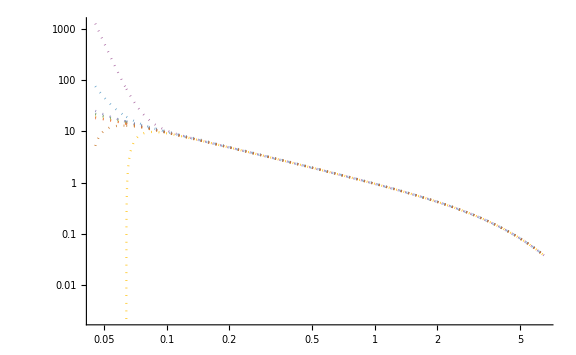

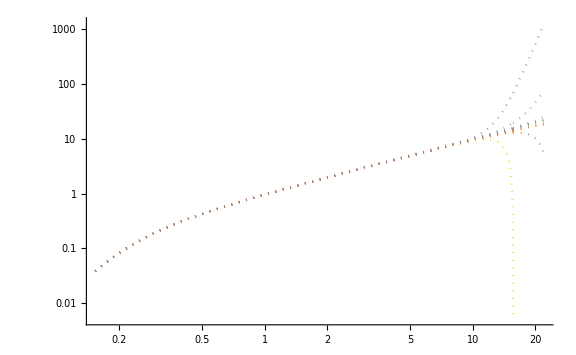

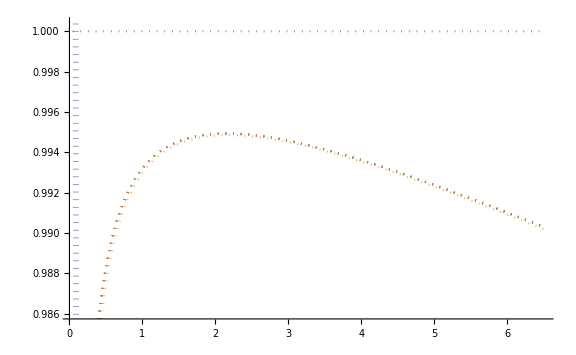

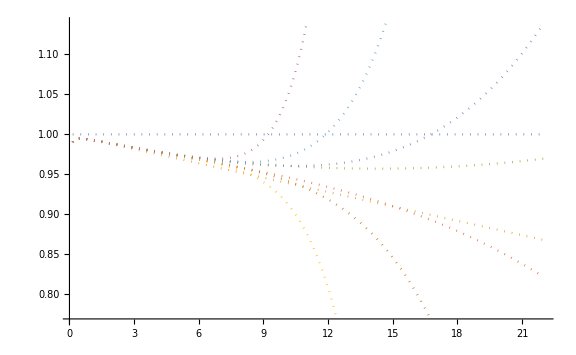

```mathematica
replConsts = {ℏ -> 1, m -> 1, ω[1] -> 1, g4[1] -> 0.002};
βMin = 1/22.0;
βMax = 6.5;

ColorData[97, "ColorList"][[1 ;; maxPowerG + 1]]

logLogPltZDirectβ = LogLogPlot[
	Evaluate[Table[ZAHODirect[β, k] /. replConsts, {k, 0, maxPowerG}]],
	{β, βMin, βMax},
	ImageSize -> Large,
	PlotStyle -> Dotted
]

logLogPltZDirectTemp = LogLogPlot[
	Evaluate[Table[ZAHODirect[1/kT, k] /. replConsts, {k, 0, maxPowerG}]],
	{kT, 1/βMax, 1/βMin},
	ImageSize -> Large,
	PlotStyle -> Dotted
]

pltZSeriesβ = Plot[
	Evaluate[Table[ZSeries[β, k] /. replConsts, {k, 0, maxPowerG}]],
	{β, βMin, βMax},
	ImageSize -> Large,
	PlotStyle -> Dotted
]

pltZSeriesTemp = Plot[
	Evaluate[Table[ZSeries[1/kT, k] /. replConsts, {k, 0, maxPowerG}]],
	{kT, 1/βMax, 1/βMin},
	ImageSize -> Large,
	PlotStyle -> Dotted
]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037]}

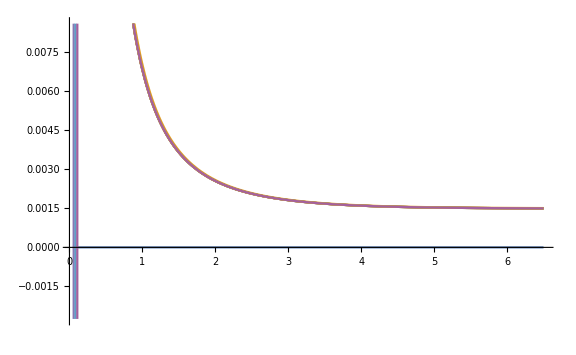

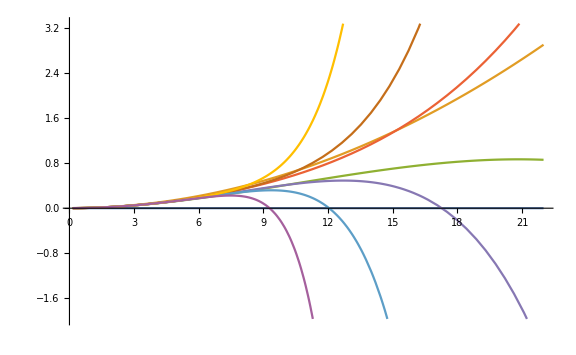

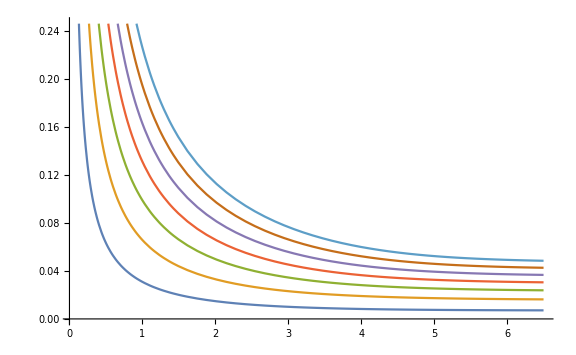

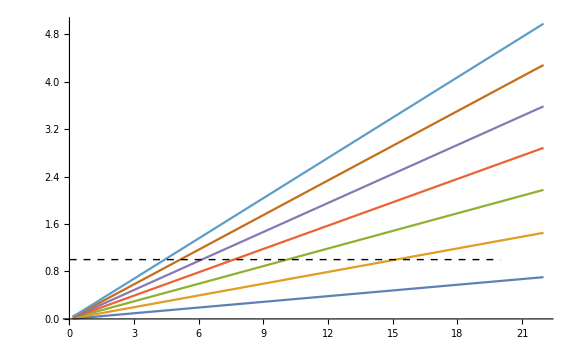

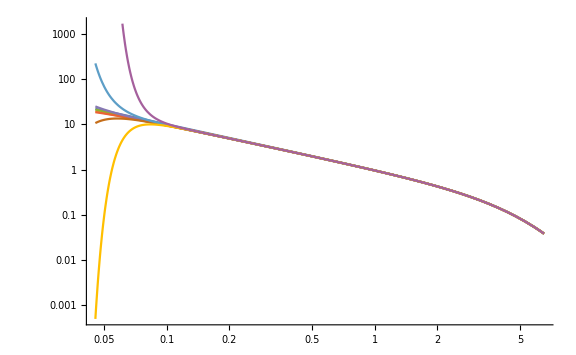

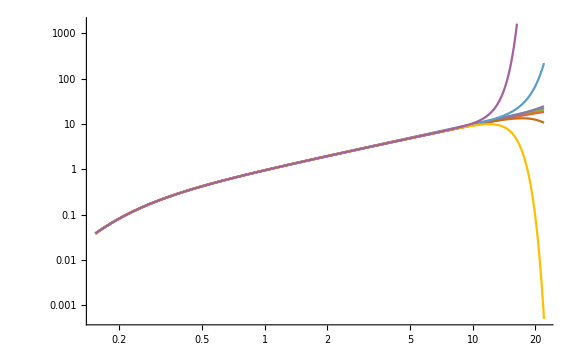

```mathematica
ClearAll[FSeries]
FSeries[β_] = Expand[Normal[Series[-Log[ZSeries[β]] / β, {g4[1], 0, maxPowerG}]]];
FSeries[β_, 0] = 0;
FSeries[β_, n_ /; 1 <= n <= maxPowerG] := FSeries[β, n] = FSeries[β] /. {g4[1]^m_ /; m > n -> 0}

FSeriesTerm[β_, 0] = 0;
FSeriesTerm[β_, n_ /; 1 <= n <= maxPowerG] := FSeries[β, n] - FSeries[β, n - 1]

ClearAll[ZAHO]
ZAHO[β_, n_ /; 0 <= n <= maxPowerG] := ZAHO[β, n] = ZHO[β] Exp[-β FSeries[β, n]]; (*Exists when n <= maxPowerG*)
ZAHO[β_, n_ /; 0 <= n <= maxPowerG, rules_] := ZAHO[β, n] /. rules;

ColorData[97, "ColorList"][[1 ;; maxPowerG + 1]]
pltFSeriesβ = Plot[
	Evaluate[Table[FSeries[β, k] /. replConsts, {k, 0, maxPowerG}]],
	{β, βMin, βMax},
	ImageSize -> Large
]

pltFSeriesTemp = Plot[
	Evaluate[Table[FSeries[1/kT, k] /. replConsts, {k, 0, maxPowerG}]],
	{kT, 1/βMax, 1/βMin},
	ImageSize -> Large
]

pltFSeriesRatiosβ = Plot[
	Evaluate[Table[Abs[FSeriesTerm[β, k + 1] / FSeriesTerm[β, k]], {k, 1, maxPowerG - 1}] /. replConsts],
	{β, βMin, βMax},
	ImageSize -> Large,
	Epilog -> {Directive[{Black, Dashed}], Line[{{0.01, 1}, {20.0, 1}}]}
]

pltFSeriesRatiosTemp = Plot[
	Evaluate[Table[Abs[FSeriesTerm[1/kT, k + 1] / FSeriesTerm[1/kT, k]], {k, 1, maxPowerG - 1}] /. replConsts],
	{kT, 1/βMax, 1/βMin},
	ImageSize -> Large,
	Epilog -> {Directive[{Black, Dashed}], Line[{{0.01, 1}, {20.0, 1}}]}
]

logLogPltZβ = LogLogPlot[
	Evaluate[Table[ZAHO[β, k] /. replConsts, {k, 0, maxPowerG}]],
	{β, βMin, βMax},
	ImageSize -> Large
]

logLogPltZTemp = LogLogPlot[
	Evaluate[Table[ZAHO[1/kT, k] /. replConsts, {k, 0, maxPowerG}]],
	{kT, 1/βMax, 1/βMin},
	ImageSize -> Large
]
```

```mathematica
(*replConstsExceptg4 = {ℏ -> 1, m -> 1, ω[1] -> 1};

ClearAll[testFreeEnergySeries, lim]

testFreeEnergySeries[β_] = Simplify[FSeries[β, maxPowerG] /. replConstsExceptg4];
lim = Expand[Limit[testFreeEnergySeries[β], β -> Infinity]]
lim == (groundStateEnergy - ℏ ω[1] / 2) /. replConstsExceptg4

ClearAll[testFreeEnergySeries, lim]*)
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037]}

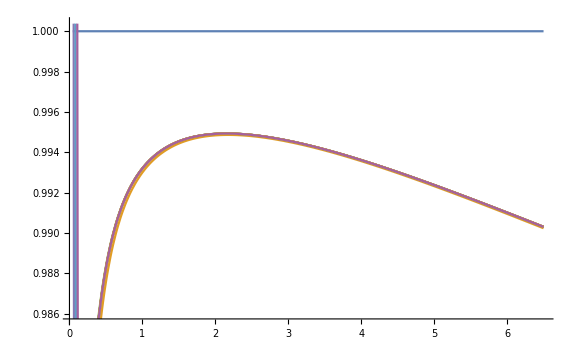

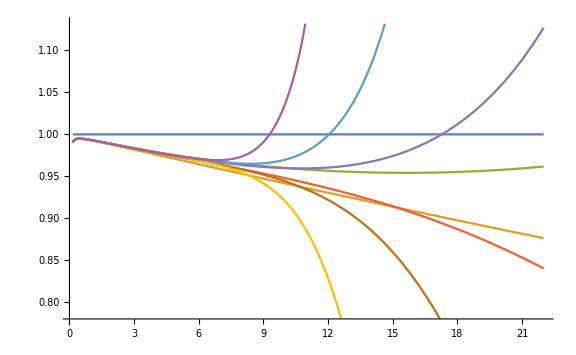

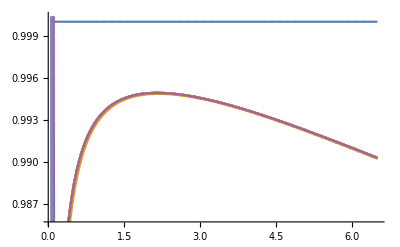

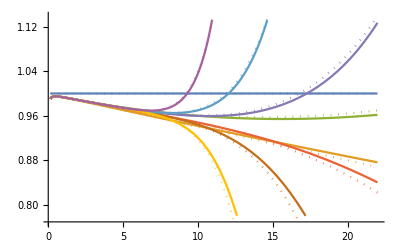

```mathematica
ColorData[97, "ColorList"][[1 ;; maxPowerG + 1]]
pltZSeriesResummedβ = Plot[
	Evaluate[Table[Exp[-β FSeries[β, k]] /. replConsts, {k, 0, maxPowerG}]],
	{β, βMin, βMax},
	ImageSize -> Large
]

pltZSeriesResummedTemp = Plot[
	Evaluate[Table[Exp[-FSeries[1/kT, k] / kT] /. replConsts, {k, 0, maxPowerG}]],
	{kT, 1/βMax, 1/βMin},
	ImageSize -> Large
]

Show[{pltZSeriesβ, pltZSeriesResummedβ}, ImageSize -> Full]
Show[{pltZSeriesTemp, pltZSeriesResummedTemp}, ImageSize -> Full]
```

```mathematica
ClearAll[ΝSeries, ΝSeriesTerm, ΝDirect, ΦSeries, ΦSeriesTerm, Ν]

saveDir = NotebookDirectory[]~StringJoin~"RateNumeratorSave.wl";
Get[saveDir];

ClearAll[RatioSeries]
Module[
	{epsilonSeries, coeffList},
	epsilonSeries[β_, ϵ_] = Collect[Normal[Series[ΝSeries[β] / ZSeries[β] /. {G4[1] -> ϵ G4[1], g4[1] -> ϵ g4[1]}, {ϵ, 0, maxPowerG}]], ϵ, Expand];
	coeffList[β_] = CoefficientList[epsilonSeries[β, ϵ], ϵ];
	RatioSeries[β_, n_] := RatioSeries[β, n] = Total[coeffList[β][[1 ;; n + 1]]]
]
RatioSeries[β_] = RatioSeries[β, maxPowerG];
```

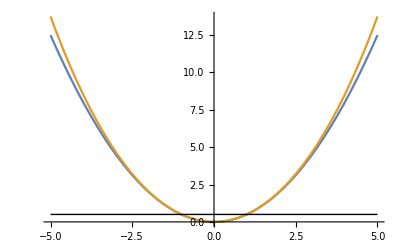

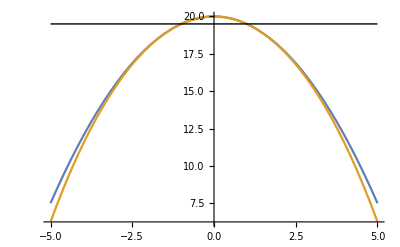

```mathematica
replConstsRate = {ℏ -> 1, m -> 1, ω[1] -> 1, g4[1] -> 0.002, λ -> 1, G4[1] -> -0.002, Esph -> 20.0};

V0[x_] := 1/2 m ω[1]^2 x^2 /. replConstsRate;
V[x_] := 1/2 m ω[1]^2 x^2 + g4[1] x^4 /. replConstsRate;

V0B[x_] := Esph - 1/2 m λ^2 x^2 /. replConstsRate;
VB[x_] := Esph - 1/2 m λ^2 x^2 + G4[1] x^4 /. replConstsRate;

Δ = 5.0;
Plot[{V0[x], V[x]}, {x, -Δ, Δ}, Epilog -> {{Directive[{Black}], Line[{{-Δ, ℏ ω[1]/2 /. replConstsRate}, {Δ, ℏ ω[1]/2 /. replConstsRate}}]}}]
Plot[{V0B[x], VB[x]}, {x, -Δ, Δ}, Epilog -> {{Directive[{Black}], Line[{{-Δ, Esph - ℏ λ /2 /. replConstsRate}, {Δ, Esph - ℏ λ/2 /. replConstsRate}}]}}]

ClearAll[ΓClassical, ΓQuantum, ΓProperSeries, Γ]

ΓClassical[β_] = (β ω[1] / (2 π)) Exp[-β Esph];

ΓQuantum[β_] = (β λ / (2 π)) Sinh[β ℏ ω[1] / 2] / Sin[β ℏ λ / 2] Exp[-β Esph];

ΓProperSeries[β_, n_ /; 0 <= n <= maxPowerG] := ΓProperSeries[β, n] = ΓQuantum[β] RatioSeries[β, n]

Γ[β_, n_ /; 0 <= n <= maxPowerG] := Γ[β, n] = ΓQuantum[β] Exp[β (FSeries[β, n] - ΦSeries[β, n])]
```

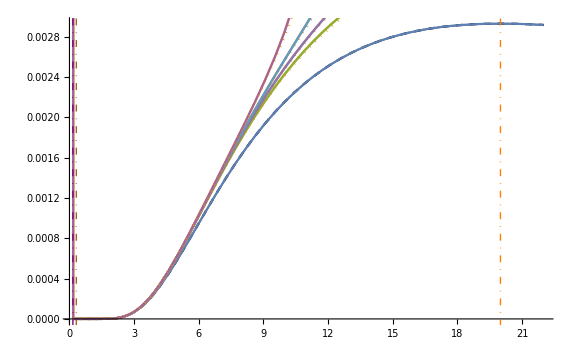

```mathematica
extraLines = {
	{Directive[{Orange, DotDashed}], Line[{{1 / Esph /. replConstsRate, -10^6}, {1 / Esph /. replConstsRate, 10^6}}]},
	{Directive[{Brown, DotDashed}], Line[{{(π) / (ℏ λ) /. replConstsRate, -10^6}, {(π) / (ℏ λ) /. replConstsRate, 10^6}}]},
	{Directive[{Purple, DotDashed}], Line[{{(2π) / (ℏ λ) /. replConstsRate, -10^6}, {(2π) / (ℏ λ) /. replConstsRate, 10^6}}]}
};

extraLines2 = {
	{Directive[{Orange, DotDashed}], Line[{{Esph /. replConstsRate, -10^6}, {Esph /. replConstsRate, 10^6}}]},
	{Directive[{Brown, DotDashed}], Line[{{ℏ λ / π /. replConstsRate, -10^6}, {ℏ λ / π /. replConstsRate, 10^6}}]},
	{Directive[{Purple, DotDashed}], Line[{{ℏ λ / (2π) /. replConstsRate, -10^6}, {ℏ λ / (2π) /. replConstsRate, 10^6}}]}
};

plt1 = Plot[
	{Evaluate[ΓClassical[1/kT] /. replConstsRate], Evaluate[ΓQuantum[1/kT] /. replConstsRate]},
	{kT, 1/βMax, 1/βMin},
	PlotStyle -> {{Black, Thin}, {Black, Dashed}},
	Epilog -> extraLines2,
	ImageSize -> Large
];

plt2 = Plot[
	Evaluate[Table[Γ[1/kT, k] /. replConstsRate, {k, 0, maxPowerG}]],
	{kT, 1/βMax, 1/βMin},
	Epilog -> extraLines2,
	ImageSize -> Large
];

plt3 = Plot[
	Evaluate[Table[ΓProperSeries[1/kT, k] /. replConstsRate, {k, 0, maxPowerG}]],
	{kT, 1/βMax, 1/βMin},
	Epilog -> extraLines2,
	ImageSize -> Large,
	PlotStyle -> Dotted
];

Show[{plt1, plt2, plt3}]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037]}

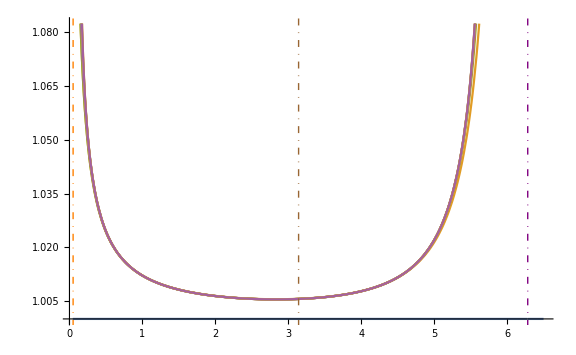

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037]}

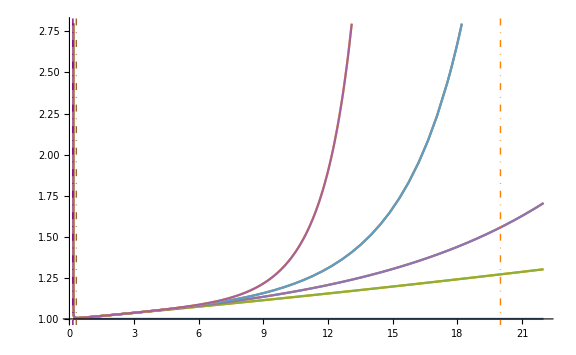

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037]}

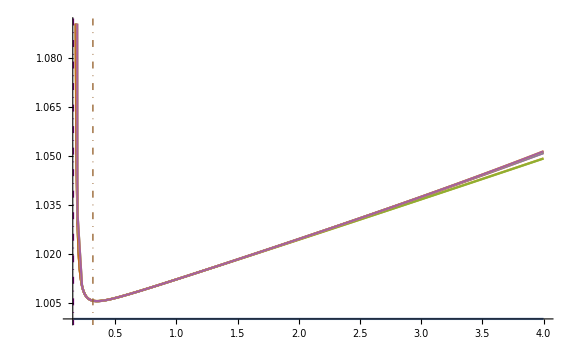

```mathematica
ClearAll[funcs]
funcs[β_] = Table[Exp[β (FSeries[β, k] - ΦSeries[β, k])] /. replConstsRate, {k, 0, maxPowerG}];
(*Exp[β FSeries[β, k]] Exp[-β ΦSeries[β, k]] is just Γ[β, k] / Γ[β, 0]*)

ColorData[97, "ColorList"][[1 ;; maxPowerG + 1]]
plt4 = Plot[
	Evaluate[funcs[β]],
	{β, βMin, βMax},
	Epilog -> extraLines,
	ImageSize -> Large
]

ColorData[97, "ColorList"][[1 ;; maxPowerG + 1]]
plt6 = Plot[
	Evaluate[funcs[1/kT]],
	{kT, 1/βMax, 1/βMin},
	Epilog -> extraLines2,
	ImageSize -> Large
]

βMinReduced = 1/4.0;
ColorData[97, "ColorList"][[1 ;; maxPowerG + 1]]
Plot[
	Evaluate[funcs[1/kT]],
	{kT, 1/βMax, 1/βMinReduced},
	Epilog -> extraLines2,
	ImageSize -> Large
]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037]}

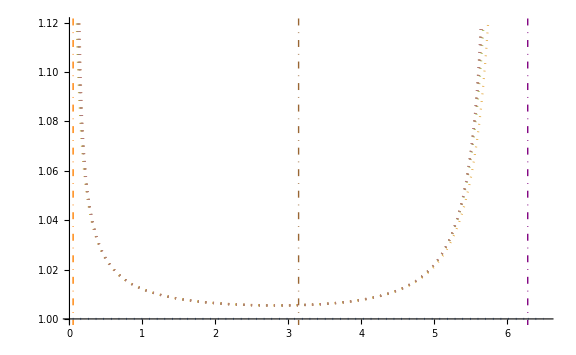

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037]}

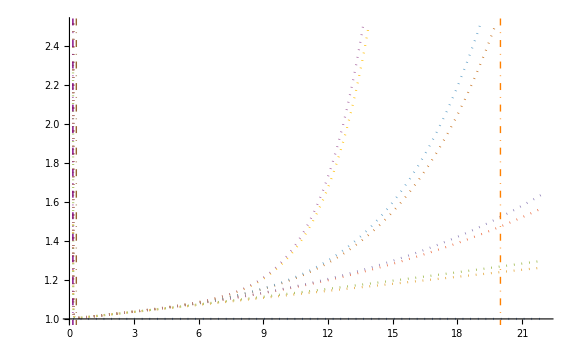

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037]}

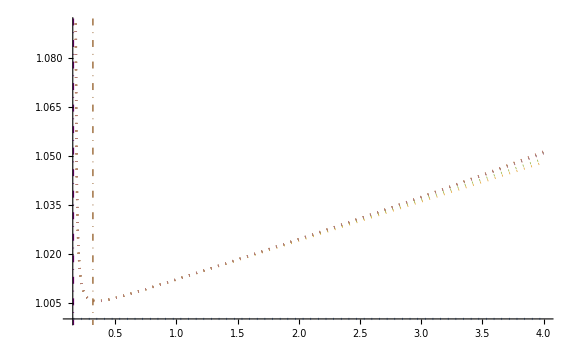

```mathematica
ClearAll[funcs2]
funcs2[β_] = Table[RatioSeries[β, k] /. replConstsRate, {k, 0, maxPowerG}];
(*ΝSeries[β, k] / ZSeries[β, k] is just ΓDirect[β, k] / ΓDirect[β, 0]*)

ColorData[97, "ColorList"][[1 ;; maxPowerG + 1]]
plt5 = Plot[
	Evaluate[funcs2[β]],
	{β, βMin, βMax},
	Epilog -> extraLines,
	ImageSize -> Large,
	PlotStyle -> Dotted
]

ColorData[97, "ColorList"][[1 ;; maxPowerG + 1]]
plt7 = Plot[
	Evaluate[funcs2[1/kT]],
	{kT, 1/βMax, 1/βMin},
	Epilog -> extraLines2,
	ImageSize -> Large,
	PlotStyle -> Dotted
]

βMinReduced = 1/4.0;
ColorData[97, "ColorList"][[1 ;; maxPowerG + 1]]
Plot[
	Evaluate[funcs2[1/kT]],
	{kT, 1/βMax, 1/βMinReduced},
	Epilog -> extraLines2,
	ImageSize -> Large,
	PlotStyle -> Dotted
]
```

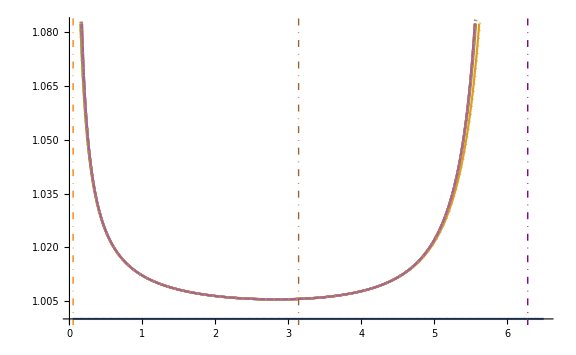

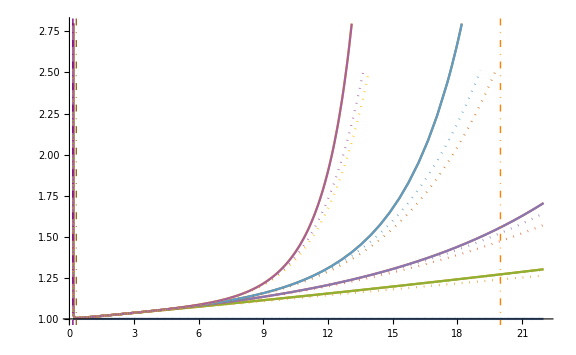

```mathematica
Show[plt4, plt5]
Show[plt6, plt7]
```

{{0,1},{1,1.0243},{2,1.02425},{3,1.02446},{4,1.02445},{5,1.02446},{6,1.02446},{7,1.02447},{8,1.02447}}

{{1.02447,1.0243},{9,2},{2,9},False}

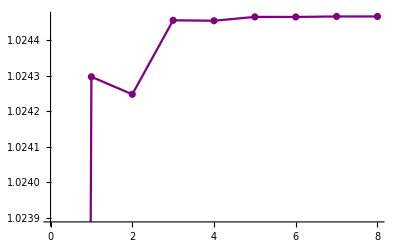

```mathematica
ClearAll[probeTemp, rateSeriesAtProbeTemp]
probeTemp = 2.0;

rateSeriesAtProbeTemp = Table[{k, Evaluate[funcs[1 / probeTemp]][[k + 1]]}, {k, 0, maxPowerG}]
intervalAsymptoticSequence[Last /@ rateSeriesAtProbeTemp]
Show[ListPlot[rateSeriesAtProbeTemp, PlotStyle -> Purple], ListLinePlot[rateSeriesAtProbeTemp, PlotStyle -> Purple]]
```

```mathematica
(*ClearAll[probeTempList, rateSeriesData]
probeTempList = Subdivide[1/βMax, 1/βMin, 100];
rateSeriesData = With[
	{intervalData = intervalAsymptoticSequence[funcs[1/#]]}, Labeled[{#, Around[intervalData[[1]]]}, {intervalData[[3]] - 1, Min[intervalData[[2]]] - 1}]
] & /@ probeTempList;

plt8 = ListPlot[
	rateSeriesData,
	ImageSize -> Large,
	Epilog -> extraLines2~Join~{Directive[{Black, Dashed}], Line[{{1/βMax, 1}, {1/βMin, 1}}]},
	PlotStyle -> Purple
]

Show[plt6, plt8]*)
```

{{0,1},{1,1.02401},{2,1.02425},{3,1.02445},{4,1.02445},{5,1.02446},{6,1.02446},{7,1.02447},{8,1.02447}}

Missing[NotFound]

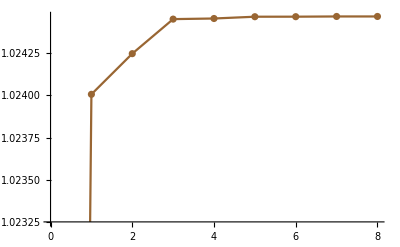

```mathematica
ClearAll[probeTemp, rateSeriesAtProbeTemp]
probeTemp = 2.0;

rateSeriesAtProbeTemp = Table[{k, Evaluate[funcs2[1 / probeTemp]][[k + 1]]}, {k, 0, maxPowerG}]
intervalAsymptoticSequence[Last /@ rateSeriesAtProbeTemp]
Show[ListPlot[rateSeriesAtProbeTemp, PlotStyle -> Brown], ListLinePlot[rateSeriesAtProbeTemp, PlotStyle -> Brown]]
```

```mathematica
(*ClearAll[probeTempList, rateSeriesData]
probeTempList = Subdivide[1/βMax, 1/βMin, 100];
rateSeriesData = With[
	{intervalData = intervalAsymptoticSequence[funcs2[1/#]]}, Labeled[{#, Around[intervalData[[1]]]}, {intervalData[[3]] - 1, Min[intervalData[[2]]] - 1}]
] & /@ probeTempList;

plt9 = ListPlot[
	rateSeriesData,
	ImageSize -> Large,
	Epilog -> extraLines2~Join~{Directive[{Black, Dashed}], Line[{{1/βMax, 1}, {1/βMin, 1}}]},
	PlotStyle -> Brown
]

Show[plt7, plt9]*)
```